```mathematica
mp321={0.9999999999992786525412331442942736314`5.,0.99892904412275687196612299313534466971`4.522568450240592,0.99884785637936350467118448725522093791`4.300815549881654,0.99703123865240754733180734393443758796`4.154071008989085,0.99695532242901555161721478112760883886`4.045081657356116,0.99682922914331474605420600161091748248`3.958004337075082,0.99681273582913446276988250762583940425`3.88553974756463,0.99679340283140976307281923641337634712`3.823452863113673,0.99674230837411027136375361518787189029`3.769127854936583,0.9966403510980885803267518674579935263`3.7208256154158184};
mi321={0.99999999999711460997989789581429915689`5.,0.98859089705341040588055975751648793332`4.51955013785888,0.98854921814198110841114368739485926348`4.299015106314121,0.98854104825416661256397007842404324083`4.153458721862969,0.98853265384770897396558838331123192595`4.044631278584338,0.98852854952424386275306208983110894658`3.9576840119822614,0.98849885497227860646844728931895722488`3.885263219417967,0.98845515753974305721505047712705577732`3.823203098477778,0.98838666378465025882810718822487932856`3.7689000661964216,0.98819570681852034030017681400142119654`3.7205843644242957};
mp322={0.9999999999992786525412331442942736314`5.,0.97294050742731369226545621335383189053`4.514900066725499,0.95030579580713411987383226185247431983`4.2880053983228406,0.94196354867976946588701256664058401357`4.14226307979894,0.92831913406403291299035967670415943748`4.030242661223142,0.91042750204892950963001889559611852483`3.938160085996421,0.88910862215210894339319931318966137184`3.863659199661585,0.88513905974167131693508477583584716113`3.7994384057357733,0.87844302172442766920012164995849987168`3.7433871019928726,0.87564664986791442064908266997187038971`3.693609589126221};
mi322={0.9999999999992786525412331442942736314`5.,0.98999973705700589906716484092877104046`4.5228786691507405,0.98948894755470993699169563374101544693`4.299458485903812,0.98433206898290227193706396555157389027`4.153345796974551,0.9799551632141654966177799871900702175`4.0420573947129235,0.97595692488075932094129936531875998794`3.955422188886651,0.97495353364502500071084036381215111368`3.882301158879878,0.97304737258767011409745492085530504488`3.819866432831246,0.97228815252406081874463452863547669022`3.765666416226989,0.97156523839832505267798546386311477527`3.7174659679039155};
mp323={0.9999999999992786525412331442942736314`5.,1.00000012022431623496439535136803617691`4.522878780089049,0.99066423878153886614617775164932104429`4.297768112647607,0.97382145330033668885839764760113705994`4.146172826381064,0.92165160718019376866591648502649226416`4.017592931384677,0.85564820479037472453383467401530900651`3.905846842460857,0.78568264711538607330673016530960690955`3.8064290075653004,0.73983082385229457895505884370110481381`3.729418040547145,0.64549257666594000042664879997968595843`3.628616883762464,0.63850624953029228082387463609078194319`3.575334257891042};
mi323={0.9999999999992786525412331442942736314`5.,0.96351332920481055765243341358998090714`4.512050842109083,0.96346328533773172551052405235174538252`4.294482799453124,0.90004498738666345845434842707405074217`4.124703275919142,0.87025192888900906877135792164909271829`4.008986516878565,0.84285113469728245764897306949122164662`3.9155612797853308,0.80646582753935496548022659107979727133`3.8315241138800924,0.80467806128904283630509503728314470831`3.768702198805212,0.8009384181258419052967004114985784007`3.709556042718428,0.79999736289844554160364200606349831102`3.654444260212695};
```

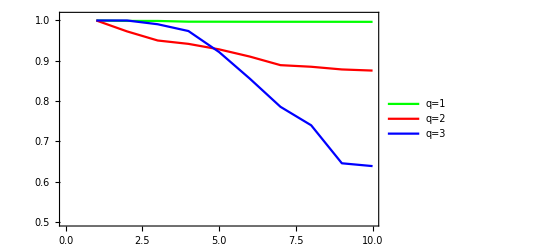

```mathematica
ListLinePlot[{mp321,mp322,mp323},PlotRange->{{0,10},{0.5,1.01}},PlotStyle->{Green,Red,Blue},Frame->True,PlotLegends->Placed[LineLegend[{Green,Red,Blue},{"q=1","q=2","q=3"},LegendFunction->"Frame"],{0.2,0.25}]]
```

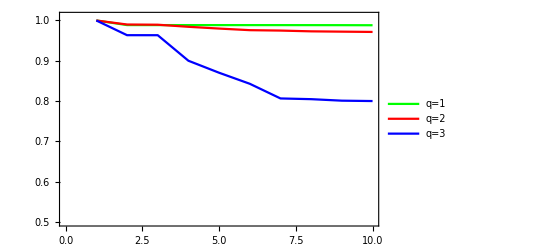

```mathematica
ListLinePlot[{mi321,mi322,mi323},PlotRange->{{0,10},{0.5,1.01}},PlotStyle->{Green,Red,Blue},Frame->True,PlotLegends->Placed[LineLegend[{Green,Red,Blue},{"q=1","q=2","q=3"},LegendFunction->"Frame"],{0.2,0.25}]]
```

```mathematica
mpv321={0.99999995740514984613825405741861466007`5.,0.998850823348854642594727856520955302`4.522545781783651,0.99880207524427220882448869217803670919`4.300813228176023,0.99803759493751436218239281968085011231`4.154462052462997,0.99798510654242597549074134291835140765`4.045394996734891,0.9979303891107240152965938838292124242`3.9582890575798944,0.99791218447874581590636167968316559628`3.8857800243201135,0.99788428540719682740076994602103566837`3.823657657581657,0.99783121887764914614447766127981131256`3.769307788826784,0.99773570965455608269900341917923432353`3.720989327780536};
miv322={0.99999994544809307886640994988284928152`5.,0.98807981992319704629164124878429900269`4.5193998509047635,0.98803316892624110349028702715631339483`4.298922892819725,0.98803242101714171299486533356562856524`4.153395562118948,0.98803083115208913783734207934499518948`4.044584775118434,0.98802343931050479389870295275565615165`3.957644630573104,0.98800988169677667074654151939589295891`3.8852364280153964,0.98798774485909999273197867393680385519`3.8231887113870378,0.98794586306315287697959319485444411493`3.768898367289583,0.9878808171332132499759617650398280595`3.7206352562058043};
miv321={0.99999939144066925261411408555646058927`5.,0.99999920718173294593929491265638517095`4.522878691931874,0.99944887703071901818301131774369233303`4.300838696062207,0.99890412129340604520081094951787311414`4.154562336497655,0.99797828982911999576531514886564320413`4.045135304801185,0.99703772045954828384211944277156921728`3.9577258510247195,0.99637960063141273638751140508047141743`3.8850459296722,0.99589385656676800740882972055174312973`3.822834962002268,0.99570470803955325336279978746608553415`3.768525837715934,0.99545837512476820104455359912607129889`3.7202271514905276};
mpv323={0.99116601023925565825700915367937196605`5.,0.98386250925291637664324370271451214284`4.520734782161844,0.92085283754624398787436965052963912648`4.276580136526698,0.91095046463299930546876486519583729467`4.133244126151082,0.89638596403926189593061202706306516766`4.022562955851998,0.88376291179649540896888482525823497732`3.93391202014078,0.87191961698242338281726780327366614052`3.8596378798586604,0.86063790331352070743142793707186826343`3.795620465797156,0.85878160267284950076666435784637282623`3.740252781680299,0.85356441161662870731809883546838355989`3.690938285508175};
mpv322={0.99999987250169677166365497856738886598`5.,0.99999986556183001510179039935092143479`4.522878743271042,0.99999972991896654828798844607117818266`4.301029947331235,0.99316693176852692914312322818334425449`4.152348421769059,0.98730803190229613724904877867825485147`4.041483987105645,0.98030193688231083978551503010065293299`3.952292887480912,0.97402746751644769033936376872610934758`3.87813031721517,0.96322751729061552035820436104137550674`3.8125047097098554,0.94565417851615989501332319105601711372`3.7519323524795527,0.94237163180104123921118042753551338008`3.6973967692321703};
miv323={0.99999984037167383368241214995944182336`5.,0.9999997835996692616056583393362332372`4.522878728843155,0.99999958671337790755710538542373963382`4.301029917396345,0.99837702589907491745694742045115626958`4.154297341004136,0.99609215422951031296630844357361378467`4.04440242935274,0.99300371659098425440434055294161572782`3.95627178765779,0.99065553155548929748748565613273646365`3.8831300582471107,0.97866352347013830530219088379238313908`3.8164305359314437,0.96715136872240762279299672630787293048`3.7581031321680967,0.96625013698137016346816104290860109883`3.7063181453254277};
```

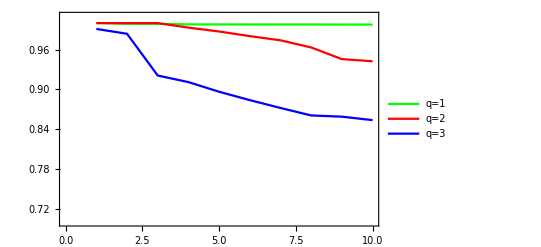

```mathematica
ListLinePlot[{mpv321,mpv322,mpv323},PlotRange->{{0,10},{0.7,1.01}},PlotStyle->{Green,Red,Blue},Frame->True,PlotLegends->Placed[LineLegend[{Green,Red,Blue},{"q=1","q=2","q=3"},LegendFunction->"Frame"],{0.2,0.25}]]
```

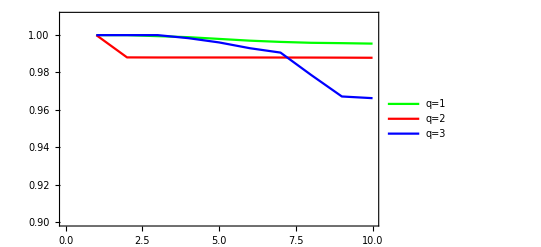

```mathematica
ListLinePlot[{miv321,miv322,miv323},PlotRange->{{0,10},{0.9,1.01}},PlotStyle->{Green,Red,Blue},Frame->True,PlotLegends->Placed[LineLegend[{Green,Red,Blue},{"q=1","q=2","q=3"},LegendFunction->"Frame"],{0.2,0.25}]]
```